```mathematica
νp=({{1, 1, 3}, {0, 0, 0}});
νr=({{0, 0, 2}, {0, 1, 1}});
S=(νp-νr);S//MatrixForm
```

(1 | 1 | 1
0 | -1 | -1)

```mathematica
MM = MatrixRank[S];
CL = Transpose@NullSpace[Transpose@S];
CC = NullSpace[S];
$Assumptions=β>1;
{NN,RR} = Dimensions[S];
SubPlus[λ][ρ_] :=SubPlus[k][ρ]Product[x[i]^νr[[i,ρ]],{i,1,NN}];SubMinus[λ][ρ_]:=SubMinus[k][ρ]Product[x[i]^νp[[i,ρ]],{i,1,NN}];
rates = { SubPlus[k][1] -> 1,SubMinus[k][1]->1,SubPlus[k] [2] ->1 , SubMinus[k][2]-> α,SubPlus[k][3]-> β,  SubMinus[k][3]->1}
J =Table[SubPlus[λ][ρ]- SubMinus[λ][ρ],{ρ,1,RR}];
J /.rates//MatrixForm
```

{k_+[1]→1,k_-[1]→1,k_+[2]→1,k_-[2]→α,k_+[3]→β,k_-[3]→1}

(1-x[1]
-α x[1]+x[2]
-x[1]^3+β x[1]^2 x[2])

```mathematica
A = S.J;A /.rates//MatrixForm
```

(1-x[1]-α x[1]-x[1]^3+x[2]+β x[1]^2 x[2]
α x[1]+x[1]^3-x[2]-β x[1]^2 x[2])

```mathematica
SubStar[x] = Solve[A == 0, Table[x[i],{i,1,NN}]][[1]];SubStar[x]/.rates //FullSimplify
```

{x[1]→1,x[2]→(1+α)/(1+β)}

```mathematica
SubStar[vecx]=Table[x[i],{i,1,NN}]/. SubStar[x]/.rates
```

{1,(1+α)/(1+β)}

```mathematica
SubStar[J]= J /. SubStar[x]; SubStar[J]/.rates//FullSimplify
```

{0,(1-α β)/(1+β),(-1+α β)/(1+β)}

```mathematica
Subscript[A, (1)] = Together@FullSimplify@Grad[A,{x[1],x[2]}]/. SubStar[x];Subscript[A, (1)]/.rates
```

{{-4-α+(2 (1+α) β)/(1+β),1+β},{3+α-(2 (1+α) β)/(1+β),-1-β}}

```mathematica
DD = FullSimplify[Det[Subscript[A, (1)]]]/.rates
```

1+β

```mathematica
T =FullSimplify[ Tr[Subscript[A, (1)]]]/.rates //Together
```

(-5-α-4 β+α β-β^2)/(1+β)

```mathematica
Subscript[s, c]= Solve[T==0,α][[1]]//FullSimplify//Together;
Subscript[α, c]= Subscript[s, c][[1,2]]
```

(5+4 β+β^2)/(-1+β)

```mathematica
(5+4 β+β^2)/(-1+β)
Plot[Subscript[α, c]]
```

(5+4 β+β^2)/(-1+β)

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[α_c]

```mathematica
Eigenvalues[Subscript[A, (1)]]/.rates/. Subscript[s, c] //FullSimplify
```

{-ⅈ √(1+β),ⅈ √(1+β)}

```mathematica
Subscript[A, Δ]=A/.Table[x[i]->SubStar[vecx][[i]]+Δx[i],{i,1,NN}]/.rates;Collect[SubStar[A],{Δx[1],Δx[2]}]
```

{-x[1] k_-[1]-x[1] k_-[2]-x[1]^3 k_-[3]+k_+[1]+x[2] k_+[2]+x[1]^2 x[2] k_+[3],x[1] k_-[2]+x[1]^3 k_-[3]-x[2] k_+[2]-x[1]^2 x[2] k_+[3]}_*

```mathematica
γ=1/2
```

1/2

```mathematica
Subscript[A, δ]=(δα)^-γ Subscript[A, Δ]/. Δx[i_]->(δα)^γ δx[i]/.α -> Subscript[α, c]+δα//FullSimplify;Collect[Subscript[A, δ],δα]
```

{((-1+β) (1+β)^2 δx[1])/(-1+β^2)+δα^(3/2) (-(β δx[1]^2)/(-1+β^2)+(β^2 δx[1]^2)/(-1+β^2))+δx[2]+β δx[2]+√δα ((3 δx[1]^2)/(-1+β^2)+(4 β δx[1]^2)/(-1+β^2)+(2 β^2 δx[1]^2)/(-1+β^2)+(β^3 δx[1]^2)/(-1+β^2)+2 β δx[1] δx[2])+δα (((-1+β)^2 δx[1])/(-1+β^2)-δx[1]^3+β δx[1]^2 δx[2]),(2 (1-β) δx[1])/(-1+β^2)+(3 (1-β) β δx[1])/(-1+β^2)+((1-β) β^2 δx[1])/(-1+β^2)+δα^(3/2) ((β δx[1]^2)/(-1+β^2)-(β^2 δx[1]^2)/(-1+β^2))-δx[2]-β δx[2]+√δα (-(3 δx[1]^2)/(-1+β^2)-(4 β δx[1]^2)/(-1+β^2)-(2 β^2 δx[1]^2)/(-1+β^2)-(β^3 δx[1]^2)/(-1+β^2)-2 β δx[1] δx[2])+δα (((-1+β) δx[1])/(-1+β^2)+((1-β) β δx[1])/(-1+β^2)+δx[1]^3-β δx[1]^2 δx[2])}

```mathematica
Subscript[M, 0]=Subscript[A, δ]/.δα->0//FullSimplify
```

{(1+β) (δx[1]+δx[2]),-((2+β) δx[1])-(1+β) δx[2]}

```mathematica
Subscript[F, δ]=Subscript[A, δ]/.δx[i_]->δx[i][t];
```

```mathematica
par = {β->3,δα->0.001}
```

{β→3,δα→0.001}

```mathematica
EQS=Table[D[δx[i][t],t]==Subscript[F, δ][[i]],{i,1,NN}]/.par;EQS//MatrixForm
IC={δx[1][0]==10,δx[2][0]==10};
vars = Table[δx[i][t],{i,1,NN}];
```

(δx[1]'[t]==1/8 δx[1][t] (32.004+1.89756 δx[1][t]-0.008 (δx[1][t])^2)+δx[2][t]+3 (1+0.0316228 δx[1][t])^2 δx[2][t]
δx[2]'[t]==1/8 δx[1][t] (-40.004-1.89756 δx[1][t]+0.008 (δx[1][t])^2)-(1+3 (1+0.0316228 δx[1][t])^2) δx[2][t])

```mathematica
Subscript[t, max]=1000;
sols=NDSolve[{EQS,IC},vars,{t,0,Subscript[t, max]}][[1]]
```

{δx[1][t]→InterpolatingFunction[…][t],δx[2][t]→InterpolatingFunction[…][t]}

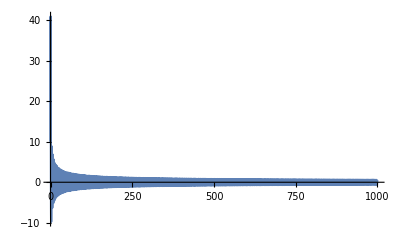

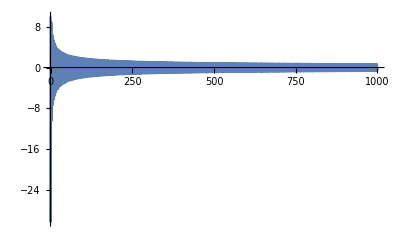

```mathematica
Plot[δx[1][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
Plot[δx[2][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
```

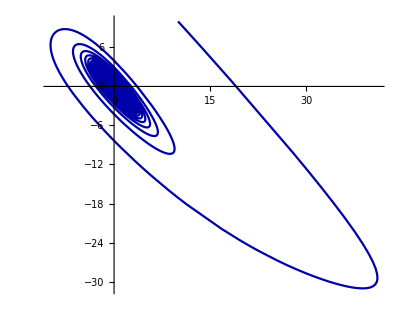

```mathematica
ParametricPlot[{δx[1][t],δx[2][t]}/.sols,{t,0,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

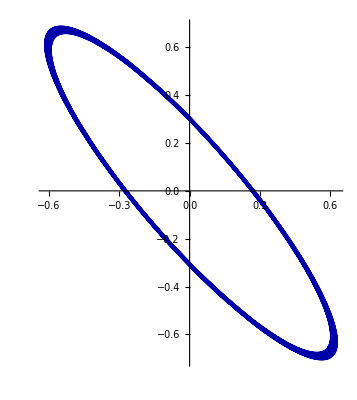

```mathematica
ParametricPlot[{δx[1][t],δx[2][t]}/.sols,{t,Subscript[t, max]*0.9,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

```mathematica
M = FullSimplify[Subscript[A, (1)]/.rates/.α->Subscript[α, c]];M//MatrixForm
```

(1+β | 1+β
-2-β | -1-β)

```mathematica
K = {{0,1},{1,0}};K//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
T=K.Inverse[Transpose[Eigenvectors[M]]];T//MatrixForm
```

(-(2+β)/(2 √(-1-β)) | -(1-√(-1-β)+β)/(2 √(-1-β))
(2+β)/(2 √(-1-β)) | (1+√(-1-β)+β)/(2 √(-1-β)))

```mathematica
T.M.Inverse[T]//FullSimplify//MatrixForm
```

(ⅈ √(1+β) | 0
0 | -ⅈ √(1+β))

```mathematica
II = {{0,1},{-1,0}};II//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
U=Inverse[Transpose[Eigenvectors[II]]];U//MatrixForm
```

(ⅈ/2 | 1/2
-ⅈ/2 | 1/2)

```mathematica
U.II.Inverse[U]//FullSimplify//MatrixForm
```

(ⅈ | 0
0 | -ⅈ)

```mathematica
vecδy = Table[δy[i],{i,1,NN}]
```

{δy[1],δy[2]}

```mathematica
vecδx = Inverse[T].U.vecδy//FullSimplify
```

{(√(1+β) δy[1]-(1+β) δy[2])/(2+β),δy[2]}

```mathematica
Subscript[A, δy]= FullSimplify@Subscript[A, δ]/.Table[δx[i]->vecδx[[i]],{i,1,NN}];Collect[Subscript[A, δy],{δy[1],δy[2]}]
```

{-((1+β)^(3/2) δα δy[1]^3)/(2+β)^3+(1+β+((1-β) (1+β) ((1+β)^2+(-1+β) δα))/((2+β) (-1+β^2))) δy[2]+(-(2 β (1+β) √δα)/(2+β)+((1+β)^2 √δα (3+β (4-δα+β (2+β+δα))))/((2+β)^2 (-1+β^2))) δy[2]^2+(((1+β)^3 δα)/(2+β)^3+(β (1+β)^2 δα)/(2+β)^2) δy[2]^3+δy[1]^2 (((1+β) √δα (3+β (4-δα+β (2+β+δα))))/((2+β)^2 (-1+β^2))+((3 (1+β)^2 δα)/(2+β)^3+(β (1+β) δα)/(2+β)^2) δy[2])+δy[1] (((-1+β) √(1+β) ((1+β)^2+(-1+β) δα))/((2+β) (-1+β^2))+((2 β √(1+β) √δα)/(2+β)-(2 (1+β)^(3/2) √δα (3+β (4-δα+β (2+β+δα))))/((2+β)^2 (-1+β^2))) δy[2]+(-(3 (1+β)^(5/2) δα)/(2+β)^3-(2 β (1+β)^(3/2) δα)/(2+β)^2) δy[2]^2),((1+β)^(3/2) δα δy[1]^3)/(2+β)^3+(-1-β+((-1+β) (1+β) (2-δα+β (3+β+δα)))/((2+β) (-1+β^2))) δy[2]+((2 β (1+β) √δα)/(2+β)-((1+β)^2 √δα (3+β (4-δα+β (2+β+δα))))/((2+β)^2 (-1+β^2))) δy[2]^2+(-((1+β)^3 δα)/(2+β)^3-(β (1+β)^2 δα)/(2+β)^2) δy[2]^3+δy[1]^2 (((-1-β) √δα (3+β (4-δα+β (2+β+δα))))/((2+β)^2 (-1+β^2))+(-(3 (1+β)^2 δα)/(2+β)^3-(β (1+β) δα)/(2+β)^2) δy[2])+δy[1] (((1-β) √(1+β) (2-δα+β (3+β+δα)))/((2+β) (-1+β^2))+(-(2 β √(1+β) √δα)/(2+β)+(2 (1+β)^(3/2) √δα (3+β (4-δα+β (2+β+δα))))/((2+β)^2 (-1+β^2))) δy[2]+((3 (1+β)^(5/2) δα)/(2+β)^3+(2 β (1+β)^(3/2) δα)/(2+β)^2) δy[2]^2)}

```mathematica
V= FullSimplify@Inverse[U].T.Subscript[A, δy]
```

{1/(√(-1-β))ⅈ (2+β) (δy[2]+β δy[2] (1+(√δα (√(1+β) δy[1]-(1+β) δy[2]))/(2+β))^2+1/((2+β) (-1+β^2))(√(1+β) δy[1]-(1+β) δy[2]) ((-1+β) ((1+β)^2+(-1+β) δα)+(√δα (3+β (4-δα+β (2+β+δα))) (√(1+β) δy[1]-(1+β) δy[2]))/(2+β)-((-1+β^2) δα (√(1+β) δy[1]-(1+β) δy[2])^2)/(2+β)^2))+((ⅈ (1-√(-1-β)+β))/(2 √(-1-β))+(ⅈ (1+√(-1-β)+β))/(2 √(-1-β))) (1/((2+β) (-1+β^2))(√(1+β) δy[1]-(1+β) δy[2]) (-((-1+β) (2-δα+β (3+β+δα)))-(√δα (3+β (4-δα+β (2+β+δα))) (√(1+β) δy[1]-(1+β) δy[2]))/(2+β)+((-1+β^2) δα (√(1+β) δy[1]-(1+β) δy[2])^2)/(2+β)^2)-δy[2] (1+β (1+(√δα (√(1+β) δy[1]-(1+β) δy[2]))/(2+β))^2)),(-(1-√(-1-β)+β)/(2 √(-1-β))+(1+√(-1-β)+β)/(2 √(-1-β))) (1/((2+β) (-1+β^2))(√(1+β) δy[1]-(1+β) δy[2]) (-((-1+β) (2-δα+β (3+β+δα)))-(√δα (3+β (4-δα+β (2+β+δα))) (√(1+β) δy[1]-(1+β) δy[2]))/(2+β)+((-1+β^2) δα (√(1+β) δy[1]-(1+β) δy[2])^2)/(2+β)^2)-δy[2] (1+β (1+(√δα (√(1+β) δy[1]-(1+β) δy[2]))/(2+β))^2))}

```mathematica
O1 = FullSimplify@Series[V,{δα,0,2}]
```

{√(1+β) δy[2]+((√(1+β) δy[1]-(1+β) δy[2]) (√(1+β) (3+β+β^2) δy[1]+(-3-8 β+β^3) δy[2]) √δα)/((-1+β) √(1+β) (2+β)^2)+1/((1+β)^(3/2) (2+β)^3)(√(1+β) δy[1]-(1+β) δy[2]) (-4+3 β^2+β^3-(1+β)^2 δy[1]^2+2 √(1+β) δy[1] δy[2]+6 β √(1+β) δy[1] δy[2]+5 β^2 √(1+β) δy[1] δy[2]+β^3 √(1+β) δy[1] δy[2]-δy[2]^2-5 β δy[2]^2-8 β^2 δy[2]^2-5 β^3 δy[2]^2-β^4 δy[2]^2) δα+(β (√(1+β) δy[1]-(1+β) δy[2])^2 δα^(3/2))/((1+β)^(3/2) (2+β)^2)+O[δα]^(5/2),-√(1+β) δy[1]+((-√(1+β) δy[1]+(1+β) δy[2]) (√(1+β) (3+β+β^2) δy[1]+(-3-8 β+β^3) δy[2]) √δα)/((-1+β) (2+β)^2)-1/((1+β) (2+β)^3)(-√(1+β) δy[1]+(1+β) δy[2]) (4+δy[1]^2+β (-β (3+β)+(2+β) δy[1]^2)-2 √(1+β) δy[1] δy[2]-6 β √(1+β) δy[1] δy[2]-5 β^2 √(1+β) δy[1] δy[2]-β^3 √(1+β) δy[1] δy[2]+(1+β)^2 (1+β (3+β)) δy[2]^2) δα-(β (√(1+β) δy[1]-(1+β) δy[2])^2 δα^(3/2))/((1+β) (2+β)^2)+O[δα]^(5/2)}

```mathematica
Subscript[F, 0]=Simplify@Coefficient[O1,δα,1/2]//FullSimplify
```

{((√(1+β) δy[1]-(1+β) δy[2]) (√(1+β) (3+β+β^2) δy[1]+(-3-8 β+β^3) δy[2]))/((-1+β) √(1+β) (2+β)^2),((-√(1+β) δy[1]+(1+β) δy[2]) (√(1+β) (3+β+β^2) δy[1]+(-3-8 β+β^3) δy[2]))/((-1+β) (2+β)^2)}

```mathematica
Subscript[F, 1]=Simplify@Coefficient[O1,δα,1]//FullSimplify
```

{1/((1+β)^(3/2) (2+β)^3)(√(1+β) δy[1]-(1+β) δy[2]) (-4+3 β^2+β^3-(1+β)^2 δy[1]^2+2 √(1+β) δy[1] δy[2]+6 β √(1+β) δy[1] δy[2]+5 β^2 √(1+β) δy[1] δy[2]+β^3 √(1+β) δy[1] δy[2]-δy[2]^2-5 β δy[2]^2-8 β^2 δy[2]^2-5 β^3 δy[2]^2-β^4 δy[2]^2),-1/((1+β) (2+β)^3)(-√(1+β) δy[1]+(1+β) δy[2]) (4+δy[1]^2+β (-β (3+β)+(2+β) δy[1]^2)-2 √(1+β) δy[1] δy[2]-6 β √(1+β) δy[1] δy[2]-5 β^2 √(1+β) δy[1] δy[2]-β^3 √(1+β) δy[1] δy[2]+(1+β)^2 (1+β (3+β)) δy[2]^2)}

```mathematica
Subscript[f, 10]=Coefficient[Subscript[F, 1],δy[2]]
```

{(4+4 β-3 β^2-4 β^3-β^4+3 δy[1]^2+11 β δy[1]^2+14 β^2 δy[1]^2+7 β^3 δy[1]^2+β^4 δy[1]^2)/((1+β)^(3/2) (2+β)^3),-(4+4 β-3 β^2-4 β^3-β^4+3 δy[1]^2+11 β δy[1]^2+14 β^2 δy[1]^2+7 β^3 δy[1]^2+β^4 δy[1]^2)/((1+β) (2+β)^3)}

```mathematica
Subscript[F, 2]=Simplify@Coefficient[O1,δα,3/2]//FullSimplify
```

{(β (√(1+β) δy[1]-(1+β) δy[2])^2)/((1+β)^(3/2) (2+β)^2),-(β (√(1+β) δy[1]-(1+β) δy[2])^2)/((1+β) (2+β)^2)}

```mathematica
Subscript[M, 0]=FullSimplify[V/.δα->0]/.δy[i_]->δy[i][t]
```

{√(1+β) δy[2][t],-√(1+β) δy[1][t]}

```mathematica
EQSy=Table[D[δy[i][t],t]==Subscript[M, 0][[i]],{i,1,NN}];EQSy//MatrixForm
vars = Table[δy[i][t],{i,1,NN}];
```

(δy[1]'[t]==√(1+β) δy[2][t]
δy[2]'[t]==-√(1+β) δy[1][t])

```mathematica
sol0 = DSolve[EQSy~Join~{δy[1][0]==Subscript[C, 0],δy[2][0]==0},vars,t][[1]]//FullSimplify
```

{δy[1][t]→Cos[t √(1+β)] C_0,δy[2][t]→-Sin[t √(1+β)] C_0}

```mathematica
T = (2π)/Sqrt[1+β]
```

(2 π)/(√(1+β))

```mathematica
Subscript[m, 2][t_]=FullSimplify@vars.(Subscript[F, 1]/.δy[i_]->δy[i][t])/.sol0
```

1/((1+β)^(3/2) (2+β)^3)Cos[t √(1+β)] C_0 (√(1+β) Cos[t √(1+β)] C_0+(1+β) Sin[t √(1+β)] C_0) (-4+3 β^2+β^3-(1+β)^2 Cos[t √(1+β)]^2 C_0^2-2 √(1+β) Cos[t √(1+β)] Sin[t √(1+β)] C_0^2-6 β √(1+β) Cos[t √(1+β)] Sin[t √(1+β)] C_0^2-5 β^2 √(1+β) Cos[t √(1+β)] Sin[t √(1+β)] C_0^2-β^3 √(1+β) Cos[t √(1+β)] Sin[t √(1+β)] C_0^2-Sin[t √(1+β)]^2 C_0^2-5 β Sin[t √(1+β)]^2 C_0^2-8 β^2 Sin[t √(1+β)]^2 C_0^2-5 β^3 Sin[t √(1+β)]^2 C_0^2-β^4 Sin[t √(1+β)]^2 C_0^2)+1/((1+β) (2+β)^3)Sin[t √(1+β)] C_0 (-√(1+β) Cos[t √(1+β)] C_0-(1+β) Sin[t √(1+β)] C_0) (4+Cos[t √(1+β)]^2 C_0^2+2 √(1+β) Cos[t √(1+β)] Sin[t √(1+β)] C_0^2+6 β √(1+β) Cos[t √(1+β)] Sin[t √(1+β)] C_0^2+5 β^2 √(1+β) Cos[t √(1+β)] Sin[t √(1+β)] C_0^2+β^3 √(1+β) Cos[t √(1+β)] Sin[t √(1+β)] C_0^2+(1+β)^2 (1+β (3+β)) Sin[t √(1+β)]^2 C_0^2+β (-β (3+β)+(2+β) Cos[t √(1+β)]^2 C_0^2))

```mathematica
Subscript[M, 2] = Integrate[Subscript[m, 2][t],{t,0,T}]
```

-(π C_0^2 (-4 (-2+β+β^2)+3 (1+β)^3 C_0^2))/(4 (1+β)^(3/2) (2+β))

```mathematica
FullSimplify@Solve[Subscript[M, 2] ==0,Subscript[C, 0]]
```

{{C_0→0},{C_0→-(2 √((-2+β+β^2)/(1+β)^3))/(√3)},{C_0→(2 √((-2+β+β^2)/(1+β)^3))/(√3)}}

```mathematica
N@%
```

{{C_0→0.},{C_0→-1.1547 √((-2.+β+β^2)/(1.+β)^3)},{C_0→1.1547 √((-2.+β+β^2)/(1.+β)^3)}}

```mathematica
FF = V/.δy[i_]->δy[i][t];
```

```mathematica
EQSfull=Table[D[δy[i][t],t]==FF[[i]],{i,1,NN}]/.par;
ICfull = {δy[1][0]==1,δy[2][0]==2};
vars = Table[δy[i][t],{i,1,NN}];
```

```mathematica
Subscript[t, max]=10000;
solfull=NDSolve[{EQSfull,ICfull},vars,{t,0,Subscript[t, max]}][[1]]
```

{δy[1][t]→InterpolatingFunction[{{0., 10000.}}, <>][t],δy[2][t]→InterpolatingFunction[{{0., 10000.}}, <>][t]}

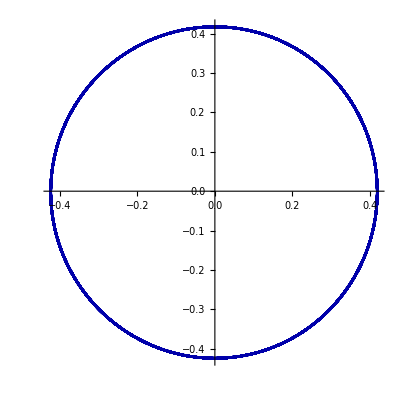

```mathematica
ParametricPlot[{δy[1][t],δy[2][t]}/.solfull,{t,Subscript[t, max]*0.9,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

```mathematica
comp ={δy[1]->(z+ζ)/2,δy[2]->(z-ζ)/(2ⅈ)}
```

{δy[1]→(z+ζ)/2,δy[2]→-1/2 ⅈ (z-ζ)}

```mathematica
$Assumptions=β>0
```

β>0

```mathematica
Vcomp = V[[1]]-ⅈ V[[2]]/.comp//FullSimplify
```

-1/(4 √(1+β) (2+β)^3 (1-β^2))ⅈ (-2 ⅈ (2+β) (-ⅈ (2+β)^3 (-1+β^2) (z-ζ)+ⅈ β (2+β) (1-β^2) (z-ζ) (2+β+1/2 √δα (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ)))^2-(ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ)) ((1-β) (2+β)^2 ((1+β)^2+(-1+β) δα)-1/2 (2+β) √δα (3+β (4-δα+β (2+β+δα))) (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ))-1/4 (1-β^2) δα (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ))^2))+2 ⅈ √(1+β) (ⅈ (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ)) ((1-β) (2+β)^2 (2-δα+β (3+β+δα))-1/2 (2+β) √δα (3+β (4-δα+β (2+β+δα))) (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ))-1/4 (1-β^2) δα (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ))^2)+(2+β) (1-β^2) (z-ζ) ((2+β)^2+β (2+β+1/2 √δα (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ)))^2))-2 (1+β) (ⅈ (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ)) ((1-β) (2+β)^2 (2-δα+β (3+β+δα))-1/2 (2+β) √δα (3+β (4-δα+β (2+β+δα))) (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ))-1/4 (1-β^2) δα (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ))^2)+(2+β) (1-β^2) (z-ζ) ((2+β)^2+β (2+β+1/2 √δα (ⅈ (1+β) (z-ζ)+√(1+β) (z+ζ)))^2)))

```mathematica
$Assumptions = {ϵ>0,z ϵ Reals,ζ ϵ Reals,β >0};
Subscript[W, 0]=Integrate[Vcomp,z]//FullSimplify
```

-1/(96 √(1+β) (2+β)^3 (1-β^2))ⅈ z (3 z^3 (-1+β) (1+β)^2 (-4 ⅈ √(1+β)+β (8-8 ⅈ √(1+β)+β (12+ⅈ √(1+β)+β (3+ⅈ √(1+β))))) δα-768 ζ+4 z^2 (1+β) (2+β) (-2 ⅈ (-6+β (-25-20 β+β^3)) √δα-2 (-1+β) β (-2 (ⅈ+√(1+β))+β (-3 ⅈ+√(1+β))) δα^(3/2)+2 (6+β (5+β (-4+β (2+β)))) √((1+β) δα)-ⅈ (-1+β^2) (-6 ⅈ+β (-12 ⅈ+5 √(1+β)+β (-5 ⅈ+3 √(1+β)))) δα ζ)+12 ζ (8 β (-20+β (-10+β (13+β (17+β (7+β)))))-32 ⅈ √(1+β) δα+16 ⅈ β √(1+β) δα+40 ⅈ β^2 √(1+β) δα-4 ⅈ β^3 √(1+β) δα-16 ⅈ β^4 √(1+β) δα-4 ⅈ β^5 √(1+β) δα+8 β √(1+β) δα^(3/2) ζ+8 β^2 √(1+β) δα^(3/2) ζ-6 β^3 √(1+β) δα^(3/2) ζ-8 β^4 √(1+β) δα^(3/2) ζ-2 β^5 √(1+β) δα^(3/2) ζ-24 √((1+β) δα) ζ-112 β √((1+β) δα) ζ-158 β^2 √((1+β) δα) ζ-78 β^3 √((1+β) δα) ζ+10 β^5 √((1+β) δα) ζ+2 β^6 √((1+β) δα) ζ-2 ⅈ (1+β) (2+β)^2 √δα (3+β (4-δα+β (2+β+δα))) ζ+6 ⅈ β √(1+β) δα ζ^2+11 ⅈ β^2 √(1+β) δα ζ^2-10 ⅈ β^4 √(1+β) δα ζ^2-6 ⅈ β^5 √(1+β) δα ζ^2-ⅈ β^6 √(1+β) δα ζ^2+(-1+β) (1+β)^2 (2+β) (2+β (4+β)) δα ζ^2)+6 z (2+β)^2 √δα (-4 (1+β)^2 (-3+(-3+β) β) (-ⅈ+√(1+β)) ζ+4 β (-1+β^2) (-ⅈ+√(1+β)) δα ζ+(-1+β) √δα (-8+3 ⅈ √(1+β) ζ^2+β^3 (1+3 ⅈ √(1+β)) ζ^2+β (-4 ⅈ √(1+β)+ζ^2+9 ⅈ √(1+β) ζ^2)+β^2 (8+4 ⅈ √(1+β)+(2+9 ⅈ √(1+β)) ζ^2))))

```mathematica
Subscript[V, 01]=FullSimplify@Collect[Subscript[F, 0]/.comp,z]
```

{1/(4 (-1+β) √(1+β) (2+β)^2)(z^2 (6 ⅈ √(1+β)+β (-7+12 ⅈ √(1+β)+β (-6+2 ⅈ √(1+β)+β (2+β))))-2 z (1+β) (2+β) (-3+(-3+β) β) ζ+(-6 ⅈ √(1+β)+β (-7-12 ⅈ √(1+β)+β (-6-2 ⅈ √(1+β)+β (2+β)))) ζ^2),1/(4 (-1+β) (2+β)^2)(z^2 (-6 ⅈ √(1+β)-β (-7+12 ⅈ √(1+β)+β (-6+2 ⅈ √(1+β)+β (2+β))))+2 z (1+β) (2+β) (-3+(-3+β) β) ζ+(6 ⅈ √(1+β)+β (7+12 ⅈ √(1+β)-β (-6-2 ⅈ √(1+β)+β (2+β)))) ζ^2)}

```mathematica
Subscript[V, 02]=FullSimplify@Collect[Subscript[F, 1]/.comp,z]
```

{1/(8 (1+β)^(3/2) (2+β)^3)(z^3 (1+β)^2 (2 (-ⅈ+√(1+β))+β (-ⅈ+7 √(1+β)+β (3 ⅈ+ⅈ β+2 √(1+β))))-z^2 (1+β)^2 (2+β) (3 (ⅈ+√(1+β))+β (7 ⅈ+3 ⅈ β+2 √(1+β))) ζ+ζ (-16 √(1+β)+12 β^2 √(1+β)+4 β^3 √(1+β)-4 ⅈ (2+β)^2 (-1+β^2)+2 √(1+β) ζ^2+11 β √(1+β) ζ^2+18 β^2 √(1+β) ζ^2+11 β^3 √(1+β) ζ^2+2 β^4 √(1+β) ζ^2-ⅈ (1+β)^2 (-2+β (-1+β (3+β))) ζ^2)+z (2+β) (4 β √(1+β)+4 β^2 √(1+β)-8 (ⅈ+√(1+β))+4 ⅈ β (-1+β (2+β))+3 ⅈ ζ^2-3 √(1+β) ζ^2-8 β √(1+β) ζ^2-7 β^2 √(1+β) ζ^2-2 β^3 √(1+β) ζ^2+ⅈ β (13+β (20+β (13+3 β))) ζ^2)),1/(8 (1+β) (2+β)^3)(-z^3 (1+β)^2 (2 (-ⅈ+√(1+β))+β (-ⅈ+7 √(1+β)+β (3 ⅈ+ⅈ β+2 √(1+β))))+z^2 (1+β)^2 (2+β) (3 (ⅈ+√(1+β))+β (7 ⅈ+3 ⅈ β+2 √(1+β))) ζ+ζ (16 √(1+β)-12 β^2 √(1+β)-4 β^3 √(1+β)+4 ⅈ (2+β)^2 (-1+β^2)-2 √(1+β) ζ^2-11 β √(1+β) ζ^2-18 β^2 √(1+β) ζ^2-11 β^3 √(1+β) ζ^2-2 β^4 √(1+β) ζ^2+ⅈ (1+β)^2 (-2+β (-1+β (3+β))) ζ^2)+z (2+β) (8 ⅈ+8 √(1+β)-4 β √(1+β)-4 β^2 √(1+β)-4 ⅈ β (-1+β (2+β))-3 ⅈ ζ^2+3 √(1+β) ζ^2+8 β √(1+β) ζ^2+7 β^2 √(1+β) ζ^2+2 β^3 √(1+β) ζ^2-ⅈ β (13+β (20+β (13+3 β))) ζ^2))}

```mathematica
Subscript[V, 03]=FullSimplify@Collect[Subscript[F, 2]/.comp,z]
```

{-(β (z^2 (β-2 ⅈ √(1+β))-2 z (2+β) ζ+(β+2 ⅈ √(1+β)) ζ^2))/(4 √(1+β) (2+β)^2),(β (z^2 (β-2 ⅈ √(1+β))-2 z (2+β) ζ+(β+2 ⅈ √(1+β)) ζ^2))/(4 (2+β)^2)}

```mathematica
Subscript[W, 00]=Subscript[W, 0]/.δα->0
```

-(ⅈ z (-768 ζ+96 β (-20+β (-10+β (13+β (17+β (7+β))))) ζ))/(96 √(1+β) (2+β)^3 (1-β^2))

```mathematica
Subscript[W, 01]=Integrate[Subscript[V, 01][[1]]-ⅈ Subscript[V, 01][[1]],z]//FullSimplify
```

1/((-1+β) √(1+β) (2+β)^2)(1/12+ⅈ/12) z (z^2 (6 √(1+β)+β (7 ⅈ+12 √(1+β)+β (-ⅈ β (2+β)+2 (3 ⅈ+√(1+β)))))+3 ⅈ z (1+β) (2+β) (-3+(-3+β) β) ζ+3 (-6 √(1+β)-12 β √(1+β)-2 β^2 √(1+β)-ⅈ β (1+β) (-7+β+β^2)) ζ^2)

```mathematica
Subscript[W, 02]=Integrate[Subscript[V, 02][[1]]-ⅈ Subscript[V, 02][[1]],z]//FullSimplify
```

1/((1+β)^(3/2) (2+β)^3)(1/96-ⅈ/96) z (3 z^3 (1+β)^2 (2 (-ⅈ+√(1+β))+β (-ⅈ+7 √(1+β)+β (3 ⅈ+ⅈ β+2 √(1+β))))-4 z^2 (1+β)^2 (2+β) (3 (ⅈ+√(1+β))+β (7 ⅈ+3 ⅈ β+2 √(1+β))) ζ+12 ζ (-16 √(1+β)+12 β^2 √(1+β)+4 β^3 √(1+β)-4 ⅈ (2+β)^2 (-1+β^2)+2 √(1+β) ζ^2+11 β √(1+β) ζ^2+18 β^2 √(1+β) ζ^2+11 β^3 √(1+β) ζ^2+2 β^4 √(1+β) ζ^2-ⅈ (1+β)^2 (-2+β (-1+β (3+β))) ζ^2)+6 z (2+β) (4 β √(1+β)+4 β^2 √(1+β)-8 (ⅈ+√(1+β))+4 ⅈ β (-1+β (2+β))+3 ⅈ ζ^2-3 √(1+β) ζ^2-8 β √(1+β) ζ^2-7 β^2 √(1+β) ζ^2-2 β^3 √(1+β) ζ^2+ⅈ β (13+β (20+β (13+3 β))) ζ^2))

```mathematica
Subscript[W, 03]=Integrate[Subscript[V, 03][[1]]-ⅈ Subscript[V, 03][[1]],z]//FullSimplify
```

((1/12+ⅈ/12) z β (z^2 (ⅈ β+2 √(1+β))-3 ⅈ z (2+β) ζ+3 (ⅈ β-2 √(1+β)) ζ^2))/(√(1+β) (2+β)^2)

```mathematica
$Assumptions=True
```

True

```mathematica
(6-6 ⅈ)/.Complex[j_,k_]->j+i k
```

6-6 i

```mathematica
ExpandAll[Subscript[W, 03]/.{z->a+i b,ζ->a-i b}]
```

((6-6 ⅈ) a^3 β)/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))+((6-6 ⅈ) a^2 b i β)/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))-((6-6 ⅈ) a b^2 i^2 β)/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))-((6-6 ⅈ) b^3 i^3 β)/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))-((1-ⅈ) a^3 β^2)/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))+((3-3 ⅈ) a^2 b i β^2)/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))-((3-3 ⅈ) a b^2 i^2 β^2)/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))-((7-7 ⅈ) b^3 i^3 β^2)/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))-((4+4 ⅈ) a^3 β √(1+β))/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))+((12+12 ⅈ) a^2 b i β √(1+β))/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))+((12+12 ⅈ) a b^2 i^2 β √(1+β))/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))-((4+4 ⅈ) b^3 i^3 β √(1+β))/(48 √(1+β)+48 β √(1+β)+12 β^2 √(1+β))

```mathematica
Collect[(Collect[ExpandAll[Subscript[W, 03]/.{z->a+i b,ζ->a-i b}]/.Complex[j_,k_]->j+i k,i]/.i^p_  -> ⅈ^p)/.Complex[d_,g_]->d+i g,i,Simplify]
```

(β (3 a^2 b (2+β-4 √(1+β))+3 a b^2 (2+β-4 √(1+β))+b^3 (6+7 β-4 √(1+β))-a^3 (-6+β+4 √(1+β))))/(12 √(1+β) (2+β)^2)+(i β (a^3 (-6+β-4 √(1+β))+3 a^2 b (2+β+4 √(1+β))-3 a b^2 (2+β+4 √(1+β))+b^3 (6+7 β+4 √(1+β))))/(12 √(1+β) (2+β)^2)